## Explore properties of Bessel Filters (for Figure 5.4)

poles of a 10th-order Bessel filter

```mathematica
Clear["Global`*"];
```

```mathematica
b[n_,k_]:= ((2 n-k)!)/(2^(n-k)(n-k)! k!);  (* see Wikipedia, Bessel filter *)
```

```mathematica
n0 = 10; b10tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

654729075/(654729075+654729075 s+310134825 s^2+91891800 s^3+18918900 s^4+2837835 s^5+315315 s^6+25740 s^7+1485 s^8+55 s^9+s^10)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s116547290756547290751FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b10poles=TransferFunctionPoles[b10tf]//N;
```

```mathematica
n0 = 2; b2tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

3/(3+3 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11331FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b2poles = TransferFunctionPoles[b2tf]
```

{{{1/2 (-3-ⅈ √3),1/2 (-3+ⅈ √3)}}}

```mathematica
n0 = 4; b4tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

105/(105+105 s+45 s^2+10 s^3+s^4)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111051051FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b4poles = TransferFunctionPoles[b4tf] // N;
```

```mathematica
n0 = 5; b5tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

945/(945+945 s+420 s^2+105 s^3+15 s^4+s^5)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s119459451FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b5poles = TransferFunctionPoles[b5tf] // N;
```

```mathematica
n0 = 6; b6tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

10395/(10395+10395 s+4725 s^2+1260 s^3+210 s^4+21 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1110395103951FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b6poles = TransferFunctionPoles[b6tf]//N;
```

```mathematica
n0 = 8; b8tf = TransferFunctionModel[b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i),s]
```

2027025/(2027025+2027025 s+945945 s^2+270270 s^3+51975 s^4+6930 s^5+630 s^6+36 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11202702520270251FalseFalseFalseAutomaticNoneAutomatic

```mathematica
b8poles = TransferFunctionPoles[b8tf]//N;
```

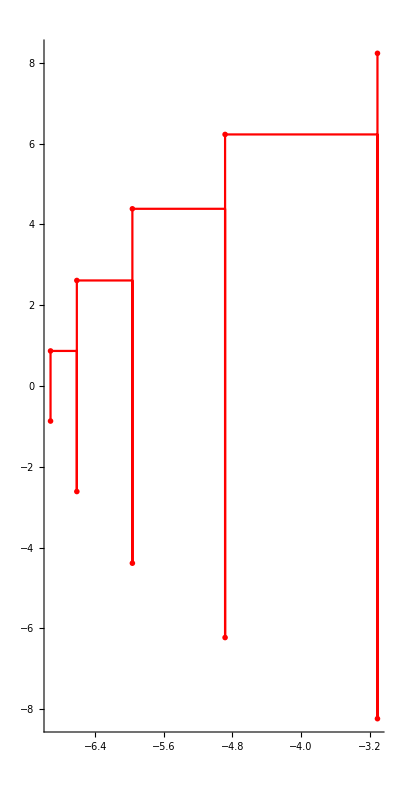

```mathematica
Show[ListPlot[Flatten[b10poles]/.Complex[x_,y_]:>{x,y},PlotMarkers->{"X",Small},PlotStyle->Red,AspectRatio->2,AxesOrigin->{0,0}],PlotRange-> All]
```

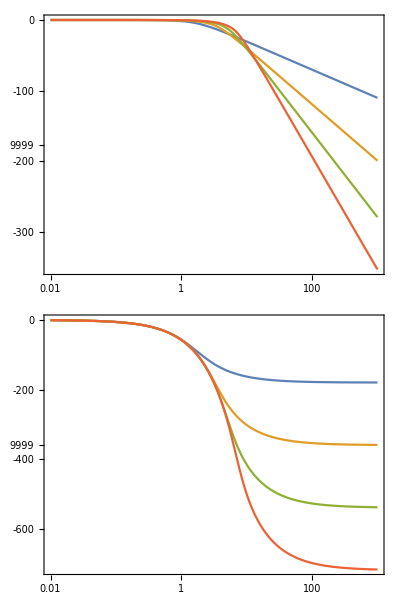

```mathematica
BodePlot[{b2tf,b4tf,b6tf,b8tf},{0.01,1000}]
```

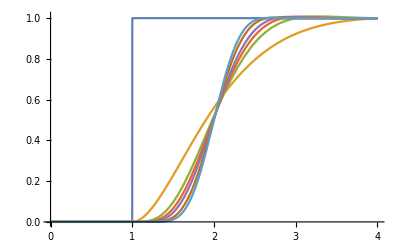

```mathematica
tmax = 10;u0 = UnitStep[t-1]- UnitStep[t-5];
y2=OutputResponse[b2tf,u0,{t,0,tmax}];
y4=OutputResponse[b4tf,u0,{t,0,tmax}];y5=OutputResponse[b5tf,u0,{t,0,tmax}];y6=OutputResponse[b6tf,u0,{t,0,tmax}];y8=OutputResponse[b8tf,u0,{t,0,tmax}];y10=OutputResponse[b10tf,u0,{t,0,tmax}];Plot[{u0,y2,y4,y5,y6,y8,y10},{t,0,4},Exclusions->None]
```

Look at state-space representations :

```mathematica
{b2sys = StateSpaceModel[b2tf],b4sys = StateSpaceModel[b4tf]}
```

{010-3-31300StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic,010000010000010-105-105-45-1011050000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic}

```mathematica
{b6sys = StateSpaceModel[b6tf],b8sys = StateSpaceModel[b8tf]}
```

{01000000010000000100000001000000010-10395-10395-4725-1260-210-21110395000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1161FalseFalseFalseAutomaticNoneAutomatic,010000000001000000000100000000010000000001000000000100000000010-2027025-2027025-945945-270270-51975-6930-630-361202702500000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1181FalseFalseFalseAutomaticNoneAutomatic}

## Look at group delay properties of Bessel filters

(this is actually how they are defined -- having the flattest group delay vs ω)

```mathematica
b2 = 3/(3+3s + s^2) /. s->I ω
```

3/(3+3 ⅈ ω-ω^2)

```mathematica
ϕ2 =ArcTan[ Refine[Im[ ComplexExpand[b2]],ω∈Reals]/Refine[Re[ ComplexExpand[b2]],ω∈Reals]]// Simplify
```

-ArcTan[(3 ω)/(3-ω^2)]

```mathematica
d2 = - D[ϕ2,ω] // Simplify
```

(3 (3+ω^2))/(9+3 ω^2+ω^4)

```mathematica
τ2 = Series[d2,{ω,0,7}]
```

1-ω^4/9+ω^6/27+O[ω]^8

```mathematica
n0 = 3; b3a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)
```

15/(15+15 s+6 s^2+s^3)

```mathematica
b3 = b3a /. s-> I ω
```

15/(15+15 ⅈ ω-6 ω^2-ⅈ ω^3)

```mathematica
ϕ3 =ArcTan[ Refine[Im[ ComplexExpand[b3]],ω∈Reals]/Refine[Re[ ComplexExpand[b3]],ω∈Reals]]// Simplify
```

ArcTan[(ω (-15+ω^2))/(15-6 ω^2)]

```mathematica
d3 = -D[ϕ3,ω]  // Simplify
```

(225+45 ω^2+6 ω^4)/(225+45 ω^2+6 ω^4+ω^6)

```mathematica
τ3 = Series[d3,{ω,0,9}]
```

1-ω^6/225+ω^8/1125+O[ω]^10

```mathematica
n0 =4; b4a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)
```

105/(105+105 s+45 s^2+10 s^3+s^4)

```mathematica
b4 = b4a /. s-> I ω
```

105/(105+105 ⅈ ω-45 ω^2-10 ⅈ ω^3+ω^4)

```mathematica
ϕ4 =ArcTan[ Refine[Im[ ComplexExpand[b4]],ω∈Reals]/Refine[Re[ ComplexExpand[b4]],ω∈Reals]]// Simplify
```

ArcTan[(5 ω (-21+2 ω^2))/(105-45 ω^2+ω^4)]

```mathematica
d4 = -D[ϕ4,ω]  // Simplify
```

(5 (2205+315 ω^2+27 ω^4+2 ω^6))/(11025+1575 ω^2+135 ω^4+10 ω^6+ω^8)

```mathematica
τ4 = Series[d4,{ω,0,11}]
```

1-ω^8/11025+ω^10/77175+O[ω]^12

```mathematica
n0 =6; b6a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)
```

10395/(10395+10395 s+4725 s^2+1260 s^3+210 s^4+21 s^5+s^6)

```mathematica
b6 = b6a /. s-> I ω
```

10395/(10395+10395 ⅈ ω-4725 ω^2-1260 ⅈ ω^3+210 ω^4+21 ⅈ ω^5-ω^6)

```mathematica
ϕ6 =ArcTan[ Refine[Im[ ComplexExpand[b6]],ω∈Reals]/Refine[Re[ ComplexExpand[b6]],ω∈Reals]]// Simplify
```

ArcTan[(21 ω (495-60 ω^2+ω^4))/(-10395+4725 ω^2-210 ω^4+ω^6)]

```mathematica
d6= -D[ϕ6,ω]  // Simplify
```

(21 (5145525+467775 ω^2+23625 ω^4+900 ω^6+30 ω^8+ω^10))/(108056025+9823275 ω^2+496125 ω^4+18900 ω^6+630 ω^8+21 ω^10+ω^12)

```mathematica
τ6 = Series[d6,{ω,0,15}]
```

1-ω^12/108056025+ω^14/1188616275+O[ω]^16

```mathematica
n0 =8; b8a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)
```

2027025/(2027025+2027025 s+945945 s^2+270270 s^3+51975 s^4+6930 s^5+630 s^6+36 s^7+s^8)

```mathematica
b8 = b8a /. s-> I ω
```

2027025/(2027025+2027025 ⅈ ω-945945 ω^2-270270 ⅈ ω^3+51975 ω^4+6930 ⅈ ω^5-630 ω^6-36 ⅈ ω^7+ω^8)

```mathematica
ϕ8 =ArcTan[ Refine[Im[ ComplexExpand[b8]],ω∈Reals]/Refine[Re[ ComplexExpand[b8]],ω∈Reals]]// Simplify
```

ArcTan[(9 ω (-225225+30030 ω^2-770 ω^4+4 ω^6))/(2027025-945945 ω^2+51975 ω^4-630 ω^6+ω^8)]

```mathematica
d8= -D[ϕ8,ω]  // Simplify
```

(9 (456536705625+30435780375 ω^2+1092566475 ω^4+28378350 ω^6+606375 ω^8+11550 ω^10+210 ω^12+4 ω^14))/(4108830350625+273922023375 ω^2+9833098275 ω^4+255405150 ω^6+5457375 ω^8+103950 ω^10+1890 ω^12+36 ω^14+ω^16)

```mathematica
τ8 = Series[d8,{ω,0,19}]
```

1-ω^16/4108830350625+ω^18/61632455259375+O[ω]^20

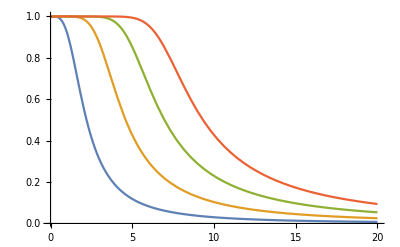

```mathematica
Plot[{d2,d4,d6,d8},{ω,0,20}]  (* group delays for different orders *)
```